# Figures for DG notes

Spring 2025

```mathematica
Needs["MaTeX`"];
SetOptions[MaTeX,"BasePreamble"->{"\\usepackage{newtx,exscale}"},FontSize->16];
```

```mathematica
ColorMapSuitePath=NotebookDirectory[]<>"/ScientificColourMaps7";
ColorMapSuite[name_String]:=ColorMapSuite[name,-1]
ColorMapSuite[name_String,el_]:=With[{list=Transpose@{Subdivide[0,1,255],RGBColor@@@First@Import[ColorMapSuitePath<>"/"<>name<>"/"<>name<>".mat"]}},Blend[list,{##}[[el]]]&]
ColorMapSuiteCategorical[name_String]:=RGBColor@@@First@Import[ColorMapSuitePath<>"/"<>name<>"/CategoricalPalettes/"<>name<>"S.mat"];
ColorMapSuiteDiscrete[name_String,n_]:=RGBColor@@@First@Import[ColorMapSuitePath<>"/"<>name<>"/DiscretePalettes/"<>name<>IntegerString[n]<>".mat"];
cols=ColorMapSuiteCategorical["batlow"];
```

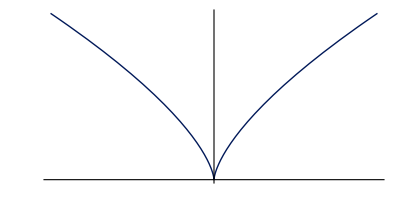

```mathematica
cusp=ParametricPlot[{t^3,t^2}, {t,-1,1},PlotStyle->{cols[[1]],Thick},Ticks->{Table[{i,MaTeX[i]},{i,-1,1}],Table[{i,MaTeX[i]},{i,0,1}]}]
```

```mathematica
Export[NotebookDirectory[]<>"cusp.pdf",cusp]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/cusp.pdf

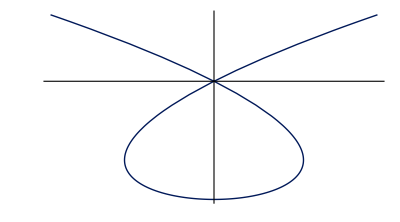

```mathematica
α[t_]:={t^3-4t,t^2-4};
conic=ParametricPlot[α[t], {t,-2.5,2.5},PlotStyle->{cols[[1]],Thick},Ticks->{Table[{i,MaTeX[i]},{i,-6,6,2}],Table[{i,MaTeX[i]},{i,-4,2,2}]}]
```

```mathematica
Export[NotebookDirectory[]<>"conic.pdf",conic]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/conic.pdf